# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\T1\\QMB_offline.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# Open boundary conditions

```mathematica
L=10;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 528

Number of odd parity eigenvectors: 496

```mathematica
L=10;
g=1.0;
J=1;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
```

```mathematica
ope=evenope+oddope;
```

```mathematica
parities=ParallelTable[Chop[Conjugate[i].ope.i],{i,eigenvec}];
```

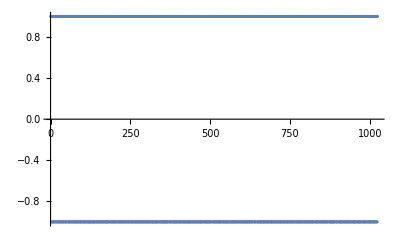

```mathematica
ListPlot[parities]
```

```mathematica
data=SortBy[Transpose[{parities,eigenval,eigenvec}],First];
```

```mathematica
neg=Count[data[[All,1]],_?Negative];
pos=Count[data[[All,1]],_?Positive];
```

```mathematica
MeanLevelSpacingRatio[data[[1;;neg,2]]]
MeanLevelSpacingRatio[data[[neg+1;;-1,2]]]
```

0.499916

0.526183

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[evenEigenvectors.H.ConjugateTranspose[evenEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
MatrixPlot[oddEigenvectors.H.ConjugateTranspose[oddEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
evenH=evenEigenvectors.H.ConjugateTranspose[evenEigenvectors];
oddH=oddEigenvectors.H.ConjugateTranspose[oddEigenvectors];
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

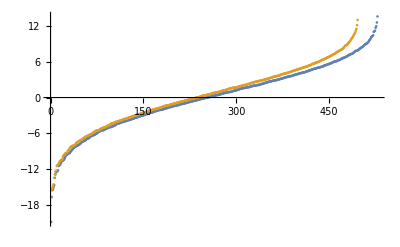

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],3000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
```

```mathematica
productstates=data[[1;;50,3]];
productstates//Dimensions
```

{50,256}

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
tlist=Table[10^i,{i,-2,20,0.005}];
tlist//Length
```

4401

```mathematica
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstates}];
```

```mathematica
newenergies=data[[1;;Length[productstates],2]];
newiprs=data[[1;;Length[productstates],1]];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstates]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstates},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed],PlotLegends->{Style["<Sd>",Black,30]}]},PlotRange->{All,All}]
```

-Graphics-

```mathematica
fakeeigenval=RandomReal[{-1,1},2^L];
fakesvntproduct=ParallelTable[{t,svn[L,La,Lb,productstates[[1]],fakeeigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
fakelongmean=Mean[fakesvntproduct[[All,2]][[-500;;-1]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
fakesvnplot=ListLogLinearPlot[fakesvntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Fake evolution",Black,25]},PlotStyle->{Directive[Purple,Opacity[0.25]]}];
```

```mathematica
Show[{plot1,fakesvnplot}]
```

-Graphics-

# Closed boundary conditions

```mathematica
L=6;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 36

Number of odd parity eigenvectors: 28

```mathematica
L=6;
g=0.0;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

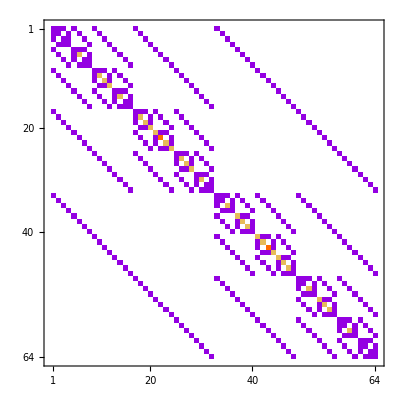

-Graphics-

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
```

```mathematica
ope=evenope+oddope;
```

```mathematica
parities=ParallelTable[Chop[Conjugate[i].ope.i],{i,eigenvec}];
```

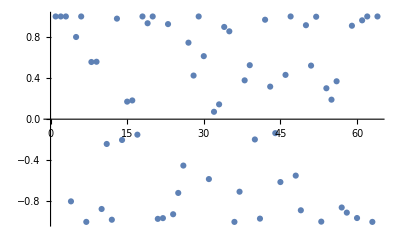

```mathematica
ListPlot[parities]
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[evenEigenvectors.H.ConjugateTranspose[evenEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
MatrixPlot[oddEigenvectors.H.ConjugateTranspose[oddEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
evenH=evenEigenvectors.H.ConjugateTranspose[evenEigenvectors];
oddH=oddEigenvectors.H.ConjugateTranspose[oddEigenvectors];
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

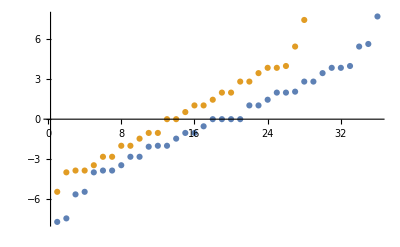

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All]
```

```mathematica
productstate2={};
Do[
uno=RandomChainProductState[1];
dos=RandomChainProductState[1];
tres=RandomChainProductState[1];
cuatro=RandomChainProductState[1];
productstate=Flatten[KroneckerProduct[uno,dos,tres,cuatro,cuatro,tres,dos,uno],1];
AppendTo[productstate2,productstate];
,{i,2000}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
```

```mathematica
productstates=data[[1;;5,3]];
productstates//Dimensions
```

{5,64}

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
tlist=Table[10^i,{i,-2,20,0.0010}];
tlist//Length
```

22001

```mathematica
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstates}];
```

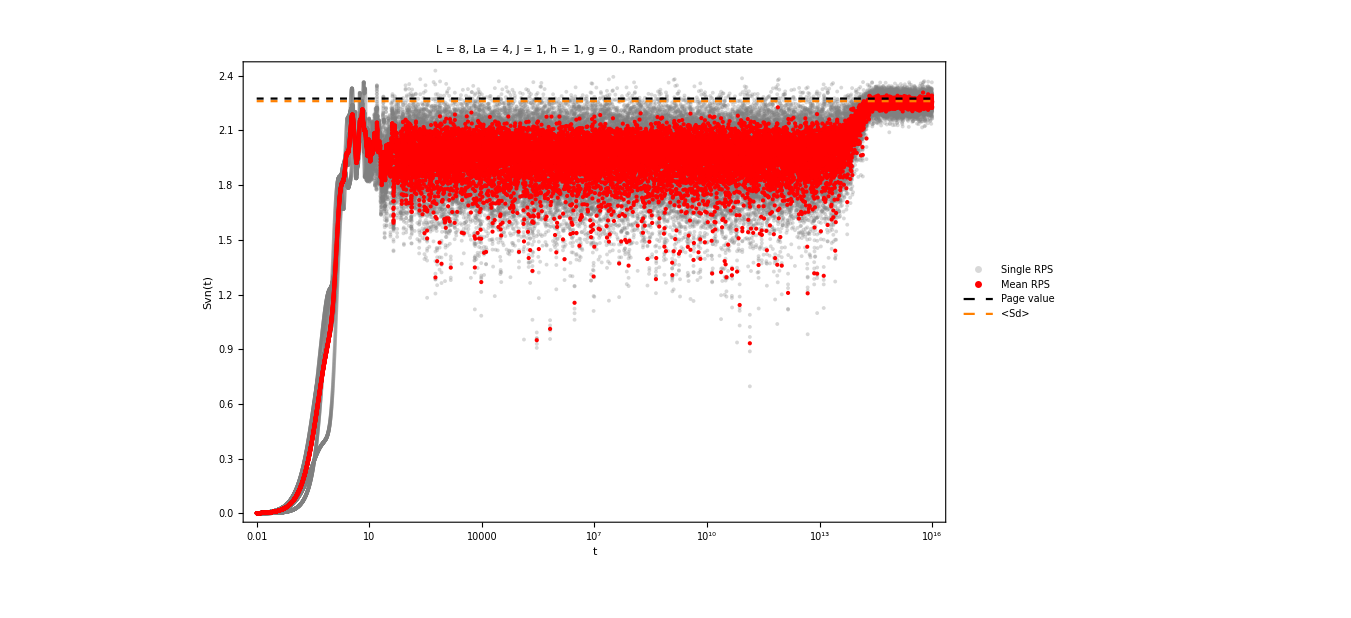

```mathematica
newenergies=data[[1;;Length[productstates],2]];
newiprs=data[[1;;Length[productstates],1]];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstates]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstates},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed],PlotLegends->{Style["<Sd>",Black,30]}]},PlotRange->{All,All}]
```

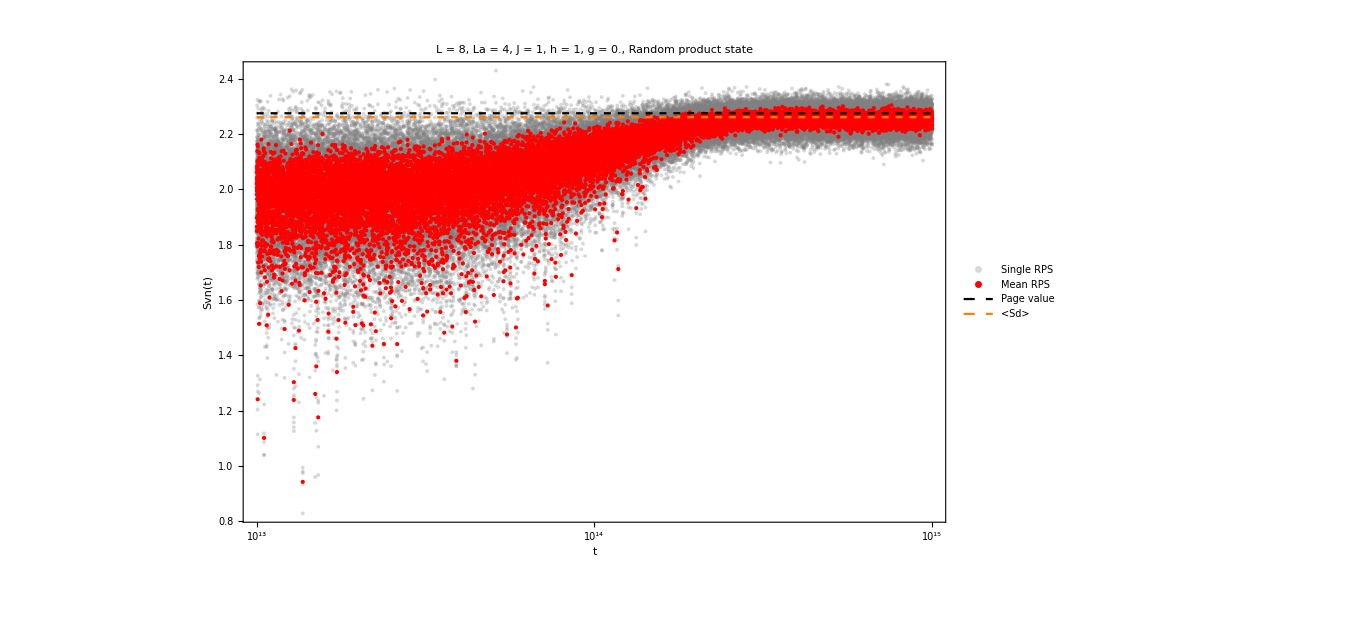

```mathematica
newenergies=data[[1;;Length[productstates],2]];
newiprs=data[[1;;Length[productstates],1]];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstates]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstates},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed],PlotLegends->{Style["<Sd>",Black,30]}]},PlotRange->{All,All}]
```

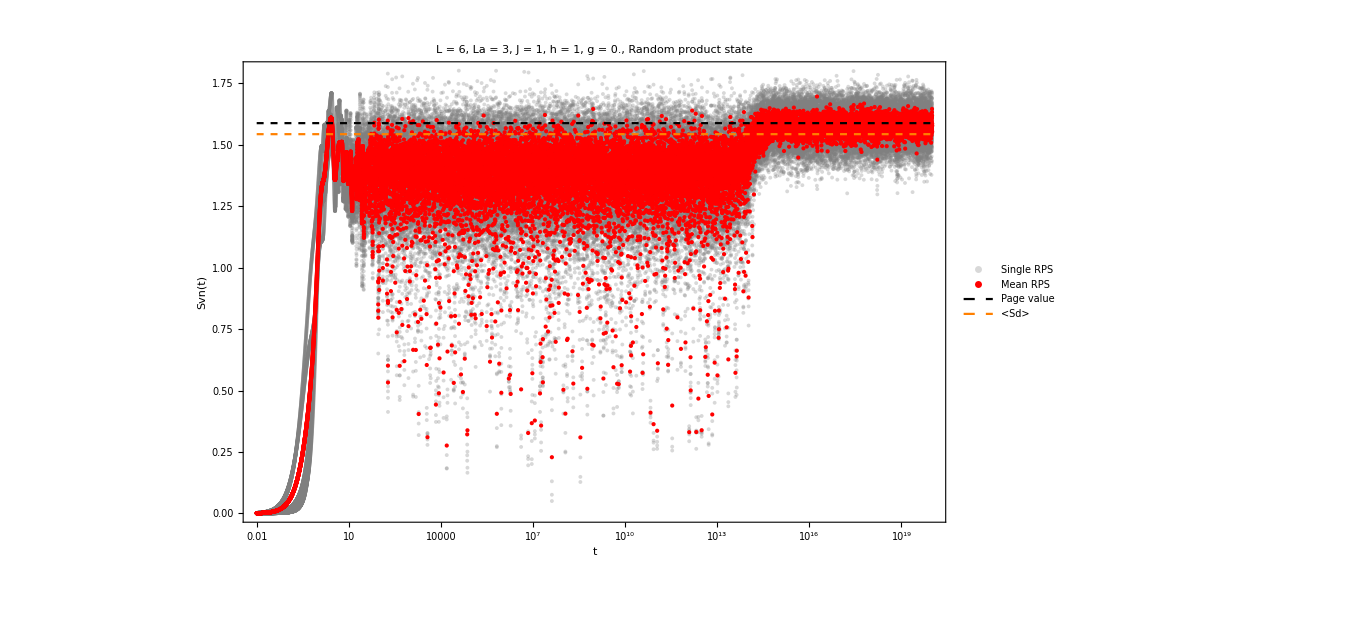

```mathematica
newenergies=data[[1;;Length[productstates],2]];
newiprs=data[[1;;Length[productstates],1]];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstates]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstates},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed],PlotLegends->{Style["<Sd>",Black,30]}]},PlotRange->{All,All}]
```

```mathematica
fakeeigenval=RandomReal[{-1,1},2^L];
fakesvntproduct=ParallelTable[{t,svn[L,La,Lb,productstates[[1]],fakeeigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
fakelongmean=Mean[fakesvntproduct[[All,2]][[-500;;-1]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
fakesvnplot=ListLogLinearPlot[fakesvntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Fake evolution",Black,25]},PlotStyle->{Directive[Purple,Opacity[0.25]]}];
```

```mathematica
Show[{plot1,fakesvnplot}]
```

```mathematica
plots=Table[ListLogLinearPlot[svntproduct[[i]],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}],{i,Length[productstates]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

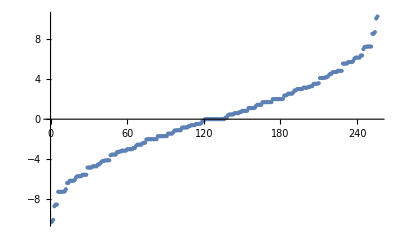

```mathematica
ListPlot[eigenval]
```

```mathematica
eigenval[[1]]
```

-7.72741

```mathematica
-7.727406610312539
```

```mathematica
g
```

0.

```mathematica
t=1;
lista=Table[Exp[-I*i*t],{i,eigenval}]
```

{0.126237+0.992 ⅈ,0.380077+0.924955 ⅈ,0.810184-0.586176 ⅈ,0.682891-0.73052 ⅈ,0.682891-0.73052 ⅈ,-0.653644-0.756802 ⅈ,-0.653644-0.756802 ⅈ,-0.750412-0.66097 ⅈ,-0.750412-0.66097 ⅈ,-0.750412-0.66097 ⅈ,-0.750412-0.66097 ⅈ,-0.948443-0.316947 ⅈ,-0.948443-0.316947 ⅈ,-0.951363+0.308072 ⅈ,-0.951363+0.308072 ⅈ,-0.951363+0.308072 ⅈ,-0.951363+0.308072 ⅈ,-0.479211+0.877699 ⅈ,-0.416147+0.909297 ⅈ,-0.416147+0.909297 ⅈ,-0.416147+0.909297 ⅈ,-0.416147+0.909297 ⅈ,0.106492+0.994314 ⅈ,0.106492+0.994314 ⅈ,0.510288+0.860003 ⅈ,0.510288+0.860003 ⅈ,0.510288+0.860003 ⅈ,0.510288+0.860003 ⅈ,0.85981+0.510614 ⅈ,1.+5.12491×10^-15 ⅈ,1.+3.28579×10^-15 ⅈ,1.-1.28614×10^-15 ⅈ,1.-1.54613×10^-15 ⅈ,1.-2.19973×10^-15 ⅈ,1.-2.84948×10^-15 ⅈ,0.85981-0.510614 ⅈ,0.510288-0.860003 ⅈ,0.510288-0.860003 ⅈ,0.510288-0.860003 ⅈ,0.510288-0.860003 ⅈ,0.106492-0.994314 ⅈ,0.106492-0.994314 ⅈ,-0.416147-0.909297 ⅈ,-0.416147-0.909297 ⅈ,-0.416147-0.909297 ⅈ,-0.416147-0.909297 ⅈ,-0.479211-0.877699 ⅈ,-0.951363-0.308072 ⅈ,-0.951363-0.308072 ⅈ,-0.951363-0.308072 ⅈ,-0.951363-0.308072 ⅈ,-0.948443+0.316947 ⅈ,-0.948443+0.316947 ⅈ,-0.750412+0.66097 ⅈ,-0.750412+0.66097 ⅈ,-0.750412+0.66097 ⅈ,-0.750412+0.66097 ⅈ,-0.653644+0.756802 ⅈ,-0.653644+0.756802 ⅈ,0.682891+0.73052 ⅈ,0.682891+0.73052 ⅈ,0.810184+0.586176 ⅈ,0.380077-0.924955 ⅈ,0.126237-0.992 ⅈ}

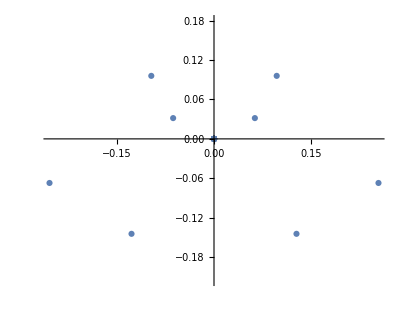

```mathematica
Differences[lista]//ComplexListPlot
```

```mathematica
t=10^15;
listb=Table[Exp[-I*i*t],{i,eigenval}]
```

{0.993474-0.114057 ⅈ,0.902175+0.431371 ⅈ,-0.37819+0.925728 ⅈ,-0.79524-0.606295 ⅈ,-0.976383-0.216047 ⅈ,0.916816-0.399309 ⅈ,-0.270196-0.962805 ⅈ,-0.965062+0.262021 ⅈ,0.987281+0.158984 ⅈ,0.903535+0.428514 ⅈ,0.292489-0.956269 ⅈ,-0.996604-0.0823479 ⅈ,-0.607761+0.79412 ⅈ,-0.86748+0.497472 ⅈ,0.813349+0.581776 ⅈ,-0.327163+0.944968 ⅈ,0.919458+0.393188 ⅈ,-0.999371-0.0354578 ⅈ,-0.761364+0.648325 ⅈ,-0.473264-0.88092 ⅈ,0.976029+0.21764 ⅈ,0.317771-0.948167 ⅈ,0.999593-0.0285437 ⅈ,-0.681794+0.731544 ⅈ,0.507297+0.861771 ⅈ,0.351851-0.936056 ⅈ,-0.842086+0.539343 ⅈ,0.850919-0.525297 ⅈ,0.348563+0.937285 ⅈ,0.400923-0.916112 ⅈ,-0.989621-0.143702 ⅈ,0.280828-0.959758 ⅈ,0.0246656-0.999696 ⅈ,-0.588282-0.808656 ⅈ,-0.957637-0.287977 ⅈ,-0.466896-0.884312 ⅈ,0.901775-0.432205 ⅈ,0.833022+0.55324 ⅈ,0.85835-0.513064 ⅈ,0.999985-0.00556565 ⅈ,-0.949051-0.315121 ⅈ,0.70539-0.708819 ⅈ,-0.996975+0.0777251 ⅈ,-0.946752+0.321964 ⅈ,0.0070072+0.999975 ⅈ,-0.761364-0.648325 ⅈ,0.782268+0.622942 ⅈ,0.637853+0.770158 ⅈ,0.637853+0.770158 ⅈ,-0.0500934-0.998745 ⅈ,-0.0500934-0.998745 ⅈ,0.534213-0.84535 ⅈ,0.975009-0.222165 ⅈ,0.491354+0.87096 ⅈ,0.903535-0.428514 ⅈ,-0.76565-0.643258 ⅈ,-0.695806+0.718229 ⅈ,0.987918-0.15498 ⅈ,-0.528457+0.84896 ⅈ,-0.695387+0.718635 ⅈ,0.228991+0.973428 ⅈ,0.72609+0.6876 ⅈ,-0.965886-0.258966 ⅈ,0.823916-0.566711 ⅈ}

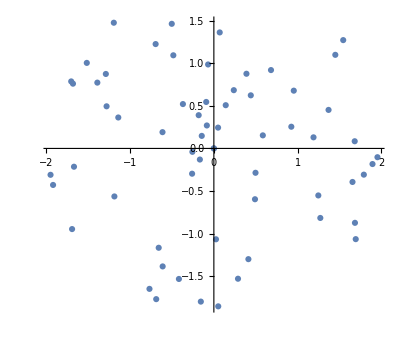

```mathematica
ComplexListPlot[Differences[listb]]
```

# Parity eigenvectors

```mathematica
L=10;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)
AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)
symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 528

Number of odd parity eigenvectors: 496

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
ope=evenope+oddope;
```

```mathematica
newH=transform.H.ConjugateTranspose[transform];
```

```mathematica
newH//Dimensions
```

{1024,1024}

```mathematica
evenEigenvectors//Length
oddEigenvectors//Length
```

528

496

```mathematica
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
evenH//Dimensions
oddH//Dimensions
```

{528,528}

{496,496}

```mathematica
MatrixPlot[evenH]
MatrixPlot[oddH]
```

-Graphics-

-Graphics-

```mathematica
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

```mathematica
MeanLevelSpacingRatio[evenval]
MeanLevelSpacingRatio[oddval]
```

0.412485

0.39634

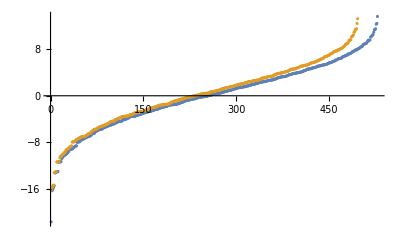

```mathematica
ListPlot[{evenval,oddval},PlotRange->All]
```

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

# Numerical precision

```mathematica
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{ck=Conjugate[eigenvec].ini,rho,dima=2^(La),dimb=2^(Lb),rhod,rhond,totalrho},
rhond=Table[If[i!=j,ck[[i]]*Conjugate[ck[[j]]*Exp[-I*Chop[eigenval[[i]]-eigenval[[j]]]*t]],ck[[i]]*Conjugate[ck[[j]]]],{i,2^L},{j,2^L}];
totalrho=ConjugateTranspose[eigenvec].(rhond).eigenvec;
rho=MatrixPartialTrace[totalrho,2,{dima,dimb}];
Chop[Total[Map[VNentropy,Chop[Eigenvalues[rho]]]]]
];
```

```mathematica
L=8;
g=0;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
ini=RandomChainProductState[L];
```

```mathematica
tlist=Table[10^i,{i,-2,17,0.0025}];
tlist//Length
```

7601

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
svnt=ParallelTable[{t,svn[L,La,Lb,ini,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
```

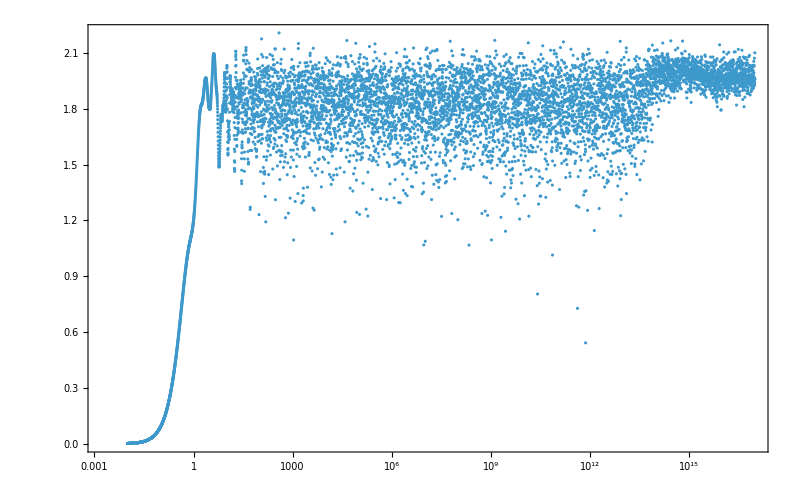

```mathematica
plot1=ListLogLinearPlot[Re[svnt],PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

# <r>

```mathematica
L=12;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)
AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)
symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 2080

Number of odd parity eigenvectors: 2016

```mathematica
h=1;
J=1;
```

```mathematica
glist=Range[0.01,2.0,0.01];
```

```mathematica
δ=7;
```

```mathematica
data={};
Do[
H=IsingNNOpenHamiltonian[h,g,J,L];
transform=Join[evenEigenvectors,oddEigenvectors];
newH=transform.H.ConjugateTranspose[transform];
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
reducedvaleven=Select[evenval,-δ<=#<=δ&];
reducedvalodd=Select[oddval,-δ<=#<=δ&];
AppendTo[data,{{h,MeanLevelSpacingRatio[reducedvaleven]},{h,MeanLevelSpacingRatio[reducedvalodd]}}];
,{g,glist}];
Export["rvalues_openchain_bothparities_L_12_h_1_g_0.01_2_delta_9.m",data];
```

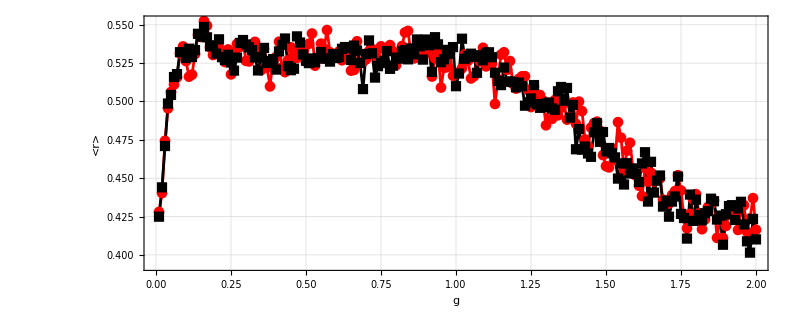

```mathematica
ListPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

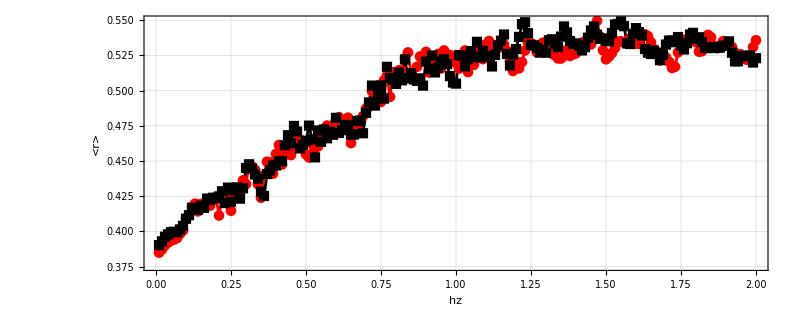

```mathematica
ListPlot[{data[[All,1]],data[[All,2]]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["hz",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

```mathematica
h=1.0;
g=2.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
transform=Join[evenEigenvectors,oddEigenvectors];
newH=transform.H.ConjugateTranspose[transform];
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

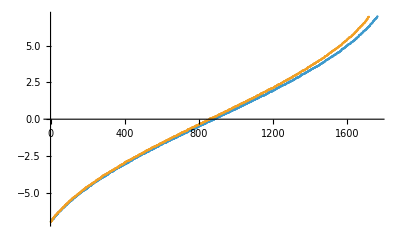

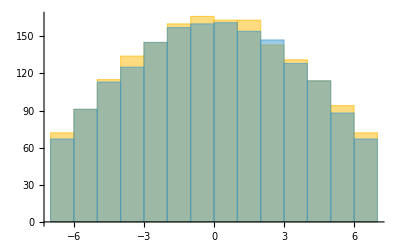

0.427987

0.424896

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```

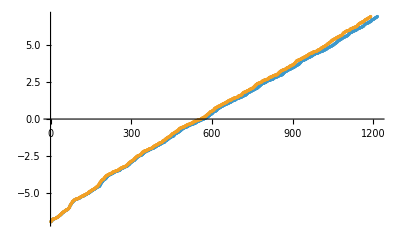

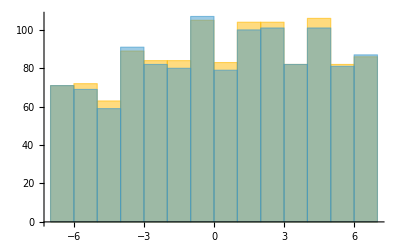

0.416349

0.410082

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```